# Frobenius solutions of Radial Teukolsky ODEs at r=r_+ and r=+\infty.

```mathematica
(*Delta[r_, a_, M_, L_] := (r^2 + a^2)(1+r^2/L^2)-2M*r *)
Delta[r_, a_, M_, L_] := r^2-2*M*r
Delta[r, a, M, L]
D[Delta[r,a,M,L],r]
```

-2 M r+r^2

-2 M+2 r

Obtain expression for the roots of D, and define a variable for the relevant one:

```mathematica
roots[a_, M_, L_] := Solve[Delta[r, a, M, L] == 0, r]
rp[a_, M_, L_] := First[r /. roots[a, M, L]]
roots[a, M, L]
```

{{r→0},{r→2 M}}

```mathematica
roots = Reduce[Delta[r,a,M,L] == 0 && r ∈ Reals, r]
```

Define the functions appearing in the Teukolsky Radial ODE:

```mathematica
mu := 1
```

```mathematica
F[r_, a_, M_, L_]:= D[Delta[r, a, M, L],r]
G[r_, a_, M_, L_, w_, m_, s_]:= (1-a^2/L^2)^2(w(r^2+a^2)-a*m)^2-ⅈ*s*(1-a^2/L^2)(w(r^2+a^2)-a*m)*D[Delta[r, a, M, L],r] 
H[r_, a_, M_, L_, w_, m_, s_, lam_] := ⅈ*4*s*w*(1-a^2/L^2)*r+2/L^2(mu+3s+2s^2)r^2+s(1+a^2/L^2)-lam+2*(1-a^2/L^2)^2*a*m*w-a^2*(1-a^2/L^2)^2*w^2
```

Obtain power series to 5th order for F, G, and H around the horizon:

```mathematica
Fseries[r_, a_, M_, L_] := Series[F[r, a, M, L], {r, rp[a, M, L], 5}]
Gseries[r_, a_, M_, L_, w_, m_, s_] := Series[G[r, a, M, L, w, m, s], {r, rp[a, M, L], 5}]
Hseries[r_, a_, M_, L_, w_, m_, s_, lam_] := Series[H[r, a, M, L, w, m, s, lam], {r, rp[a, M, L], 5}]
```

```mathematica
Fseries[r, 0.5, 1, 10]

SeriesCoefficient[Fseries[r, 0.5, 1, 10], 2]
SeriesCoefficient[Gseries[r, 0.5, 1, 10, w, m, s], 2]
SeriesCoefficient[Hseries[r, 0.5, 1, 10, w, m, s, lam], 0]
```

-2+2 r+O[r]^6

0

-0.995006 (1. m-(0.+2.00501 ⅈ) s-0.5 w) w

-lam+1.0025 s+0.995006 m w-0.248752 w^2

Use “Seriescoefficient” to actually extract the series coefficients :)

```mathematica
Fj[a_, M_, L_, j_] := SeriesCoefficient[F[r, a, M, L], {r, rp[a, M, L], j}]
Gj[a_, M_, L_, w_, m_, s_, j_] := SeriesCoefficient[G[r, a, M, L, w, m, s], {r, rp[a, M, L], j}]
Hj[a_, M_, L_, w_, m_, s_, lam_, j_] := SeriesCoefficient[H[r, a, M, L, w, m, s, lam], {r, rp[a, M, L], j}]

Fj[0.5, 1, 10, 3]
Gj[0.5, 1, 10, 1, 0, 2, 2]
Hj[0.5, 1, 10, 1, 0, 1, l, 0]
```

0

0.497503+3.99 ⅈ

0.753748-l

Fix the parameters now!

```mathematica
M = 1
a = 0.5*M
L = 10
m = 0
w = 1
s = 0

rplus = rp[0.5, 1, 10]
```

1

0.5

10

0

1

0

-0.966165-10.1395 ⅈ

```mathematica
a = 0
```

0

Compute the coefficients we need to define the indicial polynomial:

```mathematica
Fj0[j_] := SeriesCoefficient[F[r, a, M, L], {r, rplus, j}]
Gj0[j_] := SeriesCoefficient[G[r, a, M, L, w, m, s], {r, rplus, j}]
Hj0[j_] := SeriesCoefficient[H[r, a, M, L, w, m, s, lam], {r, rplus, j}]

Fj0[1]
Gj0[1]
Hj0[1]
```

2

2 ⅈ (2 M-3 rplus) rplus s w+4 rplus^3 w^2

(4 rplus (1+3 s+2 s^2))/L^2+4 ⅈ s w

Define indicial polynomial:

```mathematica
F1 = Fj0[0]
G1 = Gj0[0]
Q[n_] := n*(n-1) + F1*n + G1
```

-2 M+2 rplus

-2 ⅈ rplus^2 (-M+rplus) s w+rplus^4 w^2

6+3 (-2 M+2 rplus)-2 ⅈ rplus^2 (-M+rplus) s w+rplus^4 w^2

Find and extract the roots:

```mathematica
rplus = 2*M
indicialroots = Solve[Q[n]==0, n]
n1 = n/.indicialroots[[1]]
n2 = n/.indicialroots[[2]]
```

2 M

{{n→1/2 (1-2 M-√(1-4 M+4 M^2+32 ⅈ M^3 s w-64 M^4 w^2))},{n→1/2 (1-2 M+√(1-4 M+4 M^2+32 ⅈ M^3 s w-64 M^4 w^2))}}

1/2 (1-2 M-√(1-4 M+4 M^2+32 ⅈ M^3 s w-64 M^4 w^2))

1/2 (1-2 M+√(1-4 M+4 M^2+32 ⅈ M^3 s w-64 M^4 w^2))

Set up the recursion to find the coefficients:

```mathematica
A[0] = A0
A[k_] := A[k] = -Sum[((n1+i)*Fj0[k-i]+Gj0[k-i])*A[i],{i, 0, k-1}]/Q[n1+k]
A[1]
A[2]
A[3]
```

A0

(0.874781+3.74227 ⅈ) A0

(-0.696624-1.54911 ⅈ) A0

(1.42149+0.693754 ⅈ) A0

```mathematica
A0 = 1
```

1

6

(0.874781+3.74227 ⅈ) (-0.134002+r)^(0.112393-0.19183 ⅈ)-(0.696624+1.54911 ⅈ) (-0.134002+r)^(1.11239-0.19183 ⅈ)+(1.42149+0.693754 ⅈ) (-0.134002+r)^(2.11239-0.19183 ⅈ)-(2.03307+0.0937947 ⅈ) (-0.134002+r)^(3.11239-0.19183 ⅈ)+(0.949658-0.377576 ⅈ) (-0.134002+r)^(4.11239-0.19183 ⅈ)-(0.3486-0.466435 ⅈ) (-0.134002+r)^(5.11239-0.19183 ⅈ)

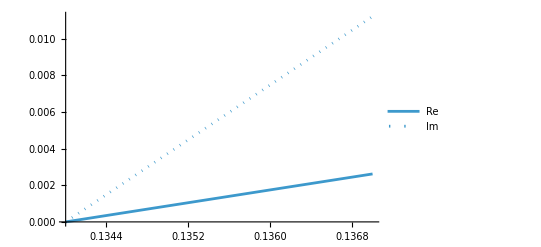

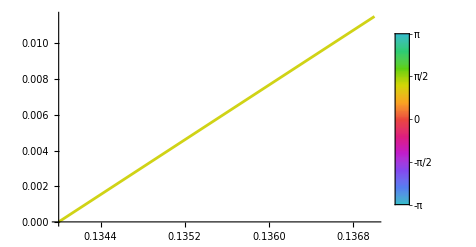

```mathematica
k = 6
Sum[A[j]*(r-rplus)^(j+n1), {j, k}]
ReImPlot[Normal[Sum[A[j]*(r-rplus)^j, {j, k}]], {r, rplus, rplus+0.003}, PlotLegends->Automatic]
AbsArgPlot[Normal[Sum[A[j]*(r-rplus)^j, {j, k}]], {r, rplus, rplus+0.003}, PlotLegends->Automatic]
```